```mathematica
Clear["Global`*"];
```

```mathematica
cplA=.3;(*heat capacity of liquid, component A, kJ/mol*K*)
cplB=.3;(*heat capacity of liquid, component B, kJ/mol*K*)
cpvA=.3;(*heat capacity of vapor, component A, kJ/mol*K*)
cpvB=.3;(*heat capacity of vapor,component B, kJ/mol*K*)

γA=12;(*heat of vaporization, component A, kJ/mol*)
γB=12; (*heat of vaporization, component B, J/mol*)
f1=77.3;
f2[x_]:=-179.43x^2+112.39x+59.96;(*bottom left - alpha liquid phase bottom line*)
f3[x_]:=-506.61x^2+815.78x-251.09;(*bottom right - beta liquid phase bottom line*)
f4[x_]:=-382.08*x^3+253.87*x^2-113.1*x+97.252;(*top left - alpha phase bubble point*)
f5[x_]:=-32.008*x^2-13.96*x+97.312;(*alpha phase dew point*)
f6[x_]:=-30*x^2+86.675*x+36.095;(*beta phase dew point*)
f7[x_]:=294.89*x^2-451.53*x+249.41;

(*top right - beta phase bubble point*)
```

```mathematica
heatαsensible1[ζ_]:=(cpvB/(cpvB+cplB)(ζ*cpvB+(1-ζ)*cpvA)+cplB/(cpvB+cplB)(ζ*cplB+(1-ζ)*cplA))*(f5[ζ]-f4[ζ]);
heatαsensible2[ζ_]:=(cpvB/(cpvB+cplB)(ζ*cpvB+(1-ζ)*cpvA)+cplB/(cpvB+cplB)(ζ*cplB+(1-ζ)*cplA))*(f5[ζ]-77.3);
heatβsensible1[ζ_]:=(cpvB/(cpvB+cplB)(ζ*cpvB+(1-ζ)*cpvA)+cplB/(cpvB+cplB)(ζ*cplB+(1-ζ)*cplA))*(f6[ζ]-77.3);
heatβsensible2[ζ_]:=(cpvB/(cpvB+cplB)(ζ*cpvB+(1-ζ)*cpvA)+cplB/(cpvB+cplB)(ζ*cplB+(1-ζ)*cplA))*(f6[ζ]-f7[ζ]);

(*Amount of heat required to reach the "horizontal line"*)
heat1liquid[ζ_]:=(77.3-70)*(ζ*cplB+(1-ζ)*cplA);


(*Amount of heat required to reach said line and fully vaporize one of two liquid phases*)
heat1alpha[ζ_]:=heat1liquid[ζ]+(ζ-0.2752)/(.6-0.2752)*(.6*γB+.4*γA);
heat1beta[ζ_]:=heat1liquid[ζ]+(.8109-ζ)/(.8109-.6)*(.6*γB+.4*γA);
```

```mathematica
heat2[ζ_]:=(f2[ζ]-70)*(ζ*cplB+(1-ζ)*cplA);
heat3[ζ_]:=(f3[ζ]-70)*(ζ*cplB+(1-ζ)*cplA);
heat4[ζ_]:=(f4[ζ]-70)*(ζ*cplB+(1-ζ)*cplA);
heat5a[ζ_]:=heat4[ζ]+ζ*γB+(1-ζ)*γA+heatαsensible1[ζ];
heat5b[ζ_]:=heat1liquid[ζ]+heatαsensible2[ζ]+ζ*γB+(1-ζ)*γA;
heat7[ζ_]:=(f7[ζ]-70)*(ζ*cplB+(1-ζ)*cplA);
heat6a[ζ_]:=heat1liquid[ζ]+heatβsensible1[ζ]+ζ*γB+(1-ζ)*γA;
heat6b[ζ_]:=heat7[ζ]+ζ*γB+(1-ζ)*γA+heatβsensible2[ζ];
```

```mathematica
model=a+b*ζ+c*ζ^2;
```

```mathematica
heat2ApproxConstants=FindFit[Table[{z,heat2[z]},{z,0.1,.276,.001}],model,{a,b,c},ζ];
heat3ApproxConstants=FindFit[Table[{z,heat3[z]},{z,.811,.92,.001}],model,{a,b,c},ζ];
heat4ApproxConstants=FindFit[Table[{z,heat4[z]},{z,0,.276,.001}],model,{a,b,c},ζ];
heat5aApproxConstants=FindFit[Table[{z,heat5a[z]},{z,0,.276,.001}],model,{a,b,c},ζ];
heat6aApproxConstants=FindFit[Table[{z,heat6a[z]},{z,.6,.811,.001}],model,{a,b,c},ζ];
heat7ApproxConstants=FindFit[Table[{z,heat7[z]},{z,.811,1,.001}],model,{a,b,c},ζ];
```

```mathematica
heat2Poly[ζ_]=Evaluate[model/.heat2ApproxConstants]
```

-3.012+33.717 ζ-53.829 ζ^2

```mathematica
heat3Poly[ζ_]=Evaluate[model/.heat3ApproxConstants]
```

-96.327+244.734 ζ-151.983 ζ^2

```mathematica
heat4Poly[ζ_]=Evaluate[model/.heat4ApproxConstants]
```

8.05641-28.7005 ζ+28.7067 ζ^2

```mathematica
heat5Poly[ζ_]=Evaluate[model/.heat5aApproxConstants]
```

20.1936-4.188 ζ-9.6024 ζ^2

```mathematica
heat6Poly[ζ_]=Evaluate[model/.heat6aApproxConstants]
```

1.8285+26.0025 ζ-9. ζ^2

```mathematica
heat7Poly[ζ_]=Evaluate[model/.heat7ApproxConstants]
```

53.823-135.459 ζ+88.467 ζ^2

```mathematica
heat2sol[H_]=NumberForm[Quiet[zsol/.Solve[H-heat2Poly[zsol]==0,zsol][[1]]],4]
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

0.00002787 (11240.-1. √(5.426×10^7-(2.392×10^7) H))

```mathematica
heat3sol[H_]=NumberForm[Quiet[zsol/.Solve[H-heat3Poly[zsol]==0,zsol][[2]]],4]
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

0.00001974 (40790.+2.828 √(4.634×10^6-(2.111×10^6) H))

```mathematica
heat4sol[H_]=NumberForm[Quiet[zsol/.Solve[H-heat4Poly[zsol]==0,zsol][[1]]],4]
```

(2.134×10^-9) (2.343×10^8-(3.495×10^-8) √(-5.529×10^30+(6.262×10^30) H))

```mathematica
heat5sol[H_]=NumberForm[Quiet[zsol/.Solve[H-heat5Poly[zsol]==0,zsol][[2]]],4]
```

0.00004166 (-5235.+1.732 √(4.131×10^8-(2.001×10^7) H))

```mathematica
heat6sol[H_]=NumberForm[Quiet[zsol/.Solve[H-heat6Poly[zsol]==0,zsol][[1]]],4]
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

0.0004167 (3467.-1. √(1.319×10^7-640000. H))

```mathematica
heat7sol[H_]=NumberForm[Quiet[zsol/.Solve[H-heat7Poly[zsol]==0,zsol][[2]]],4]
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

(5.652×10^-6) (135500.+1.732 √(-2.324×10^8+(1.18×10^8) H))

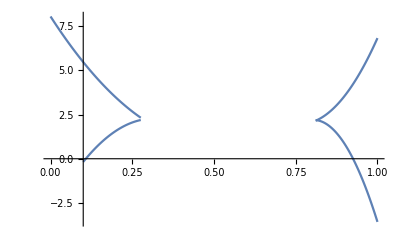

```mathematica
Show[{
Plot[heat2Poly[zed],{zed,0,.276}],
Plot[heat3Poly[zed],{zed,.811,1}],
Plot[heat4Poly[zed],{zed,0,.276}],
Plot[heat5Poly[zed],{zed,0,.276}],
Plot[heat6Poly[zed],{zed,.6,.811}],
Plot[heat7Poly[zed],{zed,.811,1}]},PlotRange->All]
```